```mathematica
(*Compute the repo root from the notebook location*)
repoRoot=ParentDirectory@NotebookDirectory[];
repoAppDir=FileNameJoin[{repoRoot,"mma"}];

If[!MemberQ[$Path,repoAppDir],AppendTo[$Path,repoAppDir];];

ClearAll["LocalF1`*"];
<<LocalF1`;
```

```mathematica
MirrorJ=((1-8 ell u^2-24 ell u^3+16 ell^2 u^4)^3)/(ell^3 u^8 (1+u-8 ell u^2-36 ell u^3-27 ell u^4+16 ell^2 u^4))
```

((1-8 ell u^2-24 ell u^3+16 ell^2 u^4)^3)/(ell^3 u^8 (1+u-8 ell u^2-36 ell u^3-27 ell u^4+16 ell^2 u^4))

```mathematica
uSol[ell_,j_]:=u/.NSolve[((1-8 ell u^2-24 ell u^3+16 ell^2 u^4)^3)/(ell^3 u^8 (1+u-8 ell u^2-36 ell u^3-27 ell u^4+16 ell^2 u^4))==j,u];
```

```mathematica
(((1-8 ell u^2-24 ell u^3+16 ell^2 u^4)^3)/(ell^3 u^8 (1+u-8 ell u^2-36 ell u^3-27 ell u^4+16 ell^2 u^4)))^(-1)//Simplify
```

(ell^3 u^8 (1+u-8 ell u^2-36 ell u^3+ell (-27+16 ell) u^4))/((1+16 ell^2 u^4-8 ell u^2 (1+3 u))^3)

```mathematica
uSolInv[ell_,jinv_]:=u/.NSolve[(ell^3 u^8 (1+u-8 ell u^2-36 ell u^3+ell (-27+16 ell) u^4))/((1+16 ell^2 u^4-8 ell u^2 (1+3 u))^3)==jinv,u];
```

```mathematica
ell1=Exp[2Pi I(-1/10)]^3//N
```

-0.309017-0.951057 ⅈ

```mathematica
uSol[ell1,1728]
```

{-0.490671+0.437362 ⅈ,-0.490671+0.437362 ⅈ,-0.117626-0.481472 ⅈ,-0.117626-0.481472 ⅈ,-0.406965+0.0146486 ⅈ,-0.406965+0.0146486 ⅈ,0.287752+0.286063 ⅈ,0.287752+0.286063 ⅈ,-0.0404619-0.286213 ⅈ,-0.0404619-0.286213 ⅈ,0.195385+0.177429 ⅈ,0.195385+0.177429 ⅈ}

```mathematica
Series[KleinInvariantJ[Log[q]/(2Pi I)],{q,0,2}]
```

1/(1728 q)+31/72+(1823 q)/16+(335840 q^2)/27+O[q]^3

```mathematica
uSolInv[ell1,0]
```

{-0.650139+0.531302 ⅈ,-0.424927+0.0173615 ⅈ,-0.041985-0.291825 ⅈ,0.198519+0.180712 ⅈ,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
lhs=Factor[MirrorJ^(-1)/.{ell->-27/256}]
```

-(19683 u^8 (64-80 u+153 u^2))/((8+9 u) (512-576 u+1080 u^2+81 u^3)^3)

```mathematica
data=Table[Thread[{s,Re[(u/.NSolve[lhs==s,u])]}], {s,-0.1,0.1,.001}];
```

```mathematica
A1=Simplify[u/.Solve[-(19683 u^8 (64-80 u+153 u^2))/((8+9 u) (512-576 u+1080 u^2+81 u^3)^3)==w,u]];
B1=Series[%,{w,0,2}];
```

Root::sbr: Because of branch cuts, the series may represent a different root of 1073741824 w-2415919104 w #1+6794772480 w #1^2-4076863488 w #1^3+3439853568 w #1^4+11179524096 w #1^5-7255941120 w #1^6+10883911680 w #1^7+(1259712+2618941248 w) #1^8+(-1574640+195570288 w) #1^9+(3011499+4782969 w) #1^10& for some values of w.

General::stop: Further output of Root::sbr will be suppressed during this calculation.

```mathematica
N[A1/.{w->10^-5},20]
```

{-0.56154579447157049046-0.2363989912635096733 ⅈ,-0.56154579447157049046+0.2363989912635096733 ⅈ,-0.1258579809640107802-0.55003326258499777985 ⅈ,-0.1258579809640107802+0.55003326258499777985 ⅈ,0.1931472656932967294-0.43651389209189701935 ⅈ,0.1931472656932967294+0.43651389209189701935 ⅈ,0.2614126053803457476-0.59150813954253372454 ⅈ,0.2614126053803457476+0.59150813954253372454 ⅈ,0.49395295995014088949-0.2694308601438543748 ⅈ,0.49395295995014088949+0.2694308601438543748 ⅈ}

```mathematica
N[Normal[B1]/.{w->10^-5},20]
```

{-0.56154851076192611467-0.2364004238732854154 ⅈ,-0.56154851076192611467+0.2364004238732854154 ⅈ,-0.1258601051076041-0.55003615247007115565 ⅈ,-0.1258601051076041+0.55003615247007115565 ⅈ,0.1931484666941290377-0.43651745483471109871 ⅈ,0.1931484666941290377+0.43651745483471109871 ⅈ,0.49395659749814320314-0.2694320088807706799 ⅈ,0.49395659749814320314+0.2694320088807706799 ⅈ,0.2614126072655430226-0.59150814388203462437 ⅈ,0.2614126072655430226+0.59150814388203462437 ⅈ}

```mathematica
B2=Re[Normal[B1]];
```

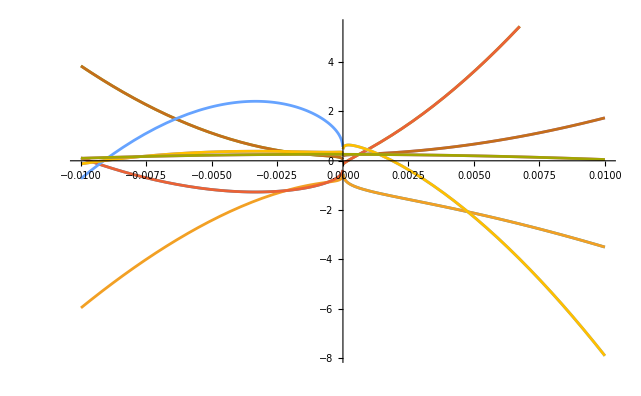

```mathematica
Plot[B2,{w,-0.01,0.01}]
```

```mathematica
MirrorJ
```

((1-8 ell u^2-24 ell u^3+16 ell^2 u^4)^3)/(ell^3 u^8 (1+u-8 ell u^2-36 ell u^3-27 ell u^4+16 ell^2 u^4))

```mathematica
Simplify[Together[MirrorJ-1728]]
```

((1-64 ell^3 u^6-12 ell u^2 (1+3 u)+24 ell^2 u^4 (2+6 u+9 u^2))^2)/(ell^3 u^8 (1+u-8 ell u^2-36 ell u^3+ell (-27+16 ell) u^4))